```mathematica
d4=1/2({{0, 1, 0, 0}, {-1, 0, 1, 0}, {0, -1, 0, 1}, {0, 0, -1, 0}})
```

{{0,1/2,0,0},{-1/2,0,1/2,0},{0,-1/2,0,1/2},{0,0,-1/2,0}}

```mathematica
d4.({{a}, {b}, {c}, {d}})
```

{{b/2},{-a/2+c/2},{-b/2+d/2},{-c/2}}

```mathematica
Eigenvectors[d4]//N
```

{{0.+1. ⅈ,-1.61803+0. ⅈ,0.-1.61803 ⅈ,1.},{0.-1. ⅈ,-1.61803+0. ⅈ,0.+1.61803 ⅈ,1.},{0.-1. ⅈ,0.618034+0. ⅈ,0.-0.618034 ⅈ,1.},{0.+1. ⅈ,0.618034+0. ⅈ,0.+0.618034 ⅈ,1.}}

```mathematica
d8=1/2({{0, 1, 0, 0, 0, 0, 0, 0}, {-1, 0, 1, 0, 0, 0, 0, 0}, {0, -1, 0, 1, 0, 0, 0, 0}, {0, 0, -1, 0, 1, 0, 0, 0}, {0, 0, 0, -1, 0, 1, 0, 0}, {0, 0, 0, 0, -1, 0, 1, 0}, {0, 0, 0, 0, 0, -1, 0, 1}, {0, 0, 0, 0, 0, 0, -1, 0}})
```

{{0,1/2,0,0,0,0,0,0},{-1/2,0,1/2,0,0,0,0,0},{0,-1/2,0,1/2,0,0,0,0},{0,0,-1/2,0,1/2,0,0,0},{0,0,0,-1/2,0,1/2,0,0},{0,0,0,0,-1/2,0,1/2,0},{0,0,0,0,0,-1/2,0,1/2},{0,0,0,0,0,0,-1/2,0}}

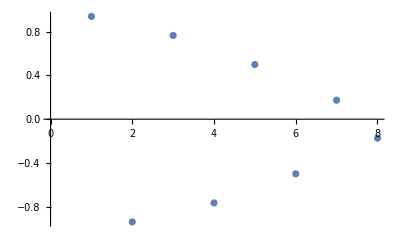

```mathematica
ListPlot[Chop[Eigenvalues[d8]/ⅈ]]
```

```mathematica
dn[n_]:=1/2Table[Table[
Which[
i==j+1,-1,
i==j-1,1,
True,0],{j,1,n}],{i,1,n}]
```

```mathematica
dn[4]//MatrixForm
```

(0 | 1/2 | 0 | 0
-1/2 | 0 | 1/2 | 0
0 | -1/2 | 0 | 1/2
0 | 0 | -1/2 | 0)

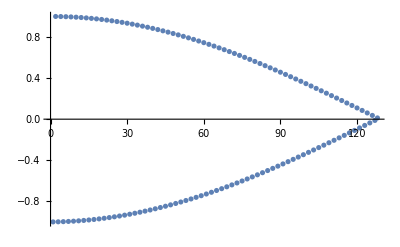

```mathematica
ListPlot[Chop[Eigenvalues[dn[128]/ⅈ]]]
```

```mathematica
MatrixPower[d4,1]//MatrixForm
```

(0 | 1/2 | 0 | 0
-1/2 | 0 | 1/2 | 0
0 | -1/2 | 0 | 1/2
0 | 0 | -1/2 | 0)

```mathematica
f=Exp[λ t+c]
```

```mathematica
D[Exp[λ t+c],{t,n}]
```

ⅇ^(c+t λ) λ^n

```mathematica
1/(2ⅈ)(Exp[ⅈ t]-Exp[-ⅈ t])
```

Sin[t]

```mathematica
sinn[n_]=1/(2ⅈ)(ⅈ^n Exp[ⅈ t]- (-ⅈ)^n Exp[-ⅈ t])
```

-1/2 ⅈ (-(-ⅈ)^n ⅇ^(-ⅈ t)+ⅈ^n ⅇ^(ⅈ t))

```mathematica
sinn[n]//FullSimplify
```

Sin[(n π)/2+t]

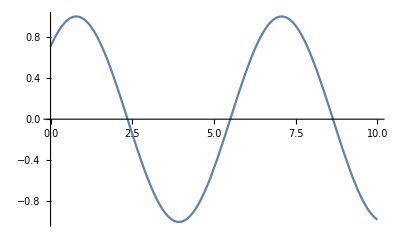

```mathematica
Plot[(Sin[t]+Cos[t])/(√2),{t,0,10}]
```

```mathematica
(* A definition of fractional derivative!  Example here on gaussian distribution.*)
```

```mathematica
FourierTransform[Exp[-x^2],x,ω]
```

(ⅇ^(-ω^2/4))/(√2)

```mathematica
dgauss[n_]=InverseFourierTransform[(-ⅈ ω)^n(ⅇ^(-ω^2/4))/(√2),ω,x]
```

1/(√π)2^n (Cos[(n π)/2] Gamma[(1+n)/2] Hypergeometric1F1[(1+n)/2,1/2,-x^2]-n x Gamma[n/2] Hypergeometric1F1[1+n/2,3/2,-x^2] Sin[(n π)/2])

```mathematica
Manipulate[Plot[dgauss[n],{x,-4,4},PlotRange->{-1,1}],{n,-4,4}]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
D[ⅇ^(-x^2),x]
```

-2 ⅇ^(-x^2) x

```mathematica
?FourierTransform
```

FourierTransform[expr,t,ω] gives the symbolic Fourier transform of expr. 
FourierTransform[expr,{t_1,t_2,…},{ω_1,ω_2,…}] gives the multidimensional Fourier transform of expr.